```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"utils.nb"}],EvaluationElements->"InitializationCell"]
```

#### defVel (implicit)

```mathematica
Options[defVel]={"DeriveParametricEquation"->True};
defVel[F_Symbol,def_Equal,OptionsPattern[]]:=Module[{},
Off[Part::partd];

(* Solve for support functions using lagrange multipliers *)
Subscript[F, bdryCnds]=def;
Subscript[σ, F]=Function[{v},Evaluate[Simplify[FullSimplify@Evaluate[Max[
{v⟦1⟧,v⟦2⟧}.{x,y}/.Solve[Eliminate[D[{v⟦1⟧,v⟦2⟧}.{x,y}-λ(#⟦2⟧-#⟦1⟧&[Subscript[F, bdryCnds]]),{{x,y,λ}}]==0,λ],{x,y}]
]],(v⟦1⟧|v⟦2⟧)∈Reals]]];
γ_(F^°)=Subscript[σ, F];
(𝒩̂)_(F^°)=Function[{ζ},Evaluate[∇_{x,y} γ_(F^°)[{x,y}]/.{x->ζ⟦1⟧,y->ζ⟦2⟧}]];(* expects pre-scaled vector on bdry(F^°)*)

(F^°)_bdryCnds=γ_(F^°)[{x,y}]==1;
σ_(F^°)=Function[{ζ},Evaluate[Simplify[FullSimplify@Evaluate[Max[
{ζ⟦1⟧,ζ⟦2⟧}.{x,y}/.Solve[Eliminate[D[{ζ⟦1⟧,ζ⟦2⟧}.{x,y}-λ(#⟦2⟧-#⟦1⟧&[(F^°)_bdryCnds]),{{x,y,λ}}]==0,λ],{x,y}]
]],(ζ⟦1⟧|ζ⟦2⟧)∈Reals]]];
Subscript[γ, F]=σ_(F^°);
Subscript[𝒩̂, F]=Function[{v},Evaluate[∇_{x,y} Subscript[γ, F][{x,y}]/.{x->v⟦1⟧,y->v⟦2⟧}]];(* expects pre-scaled vector on bdry(F)*)

Subscript[RefractedNormals, F]=Function[{ζ},Evaluate[
(* refreacted zeta must have the same tangent component as incident zeta *)
{ζ⟦1⟧,#}&/@DeleteCases[(Last/@First/@Solve[N@(F^°)_bdryCnds,{y},Reals])/.{x->ζ⟦1⟧},Undefined]
]];

If[OptionValue[DeriveParametricEquation],
(* this part needs work *)
sol=Solve[{Subscript[F, bdryCnds],Cos[t] y==Sin[t] x},{x,y},Reals];
If[Length@sol==2,
(* assume root objects split along x-axis *)
Subscript[F, bdryParam]=Simplify[Piecewise@Transpose@{{x,y}/. sol,{Pi<=t<=2 Pi,0<=t<Pi}}],
(* assume single solution *)
Subscript[F, bdryParam]={x,y}/. sol
]
];

On[Part::partd];
]
defVel[F_Symbol,def_LessEqual]:=defVel[F,def/.{LessEqual->Equal}]
```

#### Ex. 1: l_p Norms with 1<p<∞

```mathematica
defVel[F0,({x,y}.{x,y}==4)]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

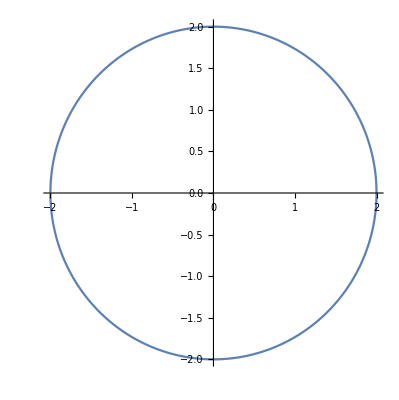

```mathematica
ParametricPlot[Subscript[F0, bdryParam],{t,0,2π}]
```

```mathematica
RegionDistance[Disk[],{x,y}]
```

Max[0,-1+√(x^2+y^2)]

```mathematica
RegionDistance[Ellipsoid[{0,0},{1,2}],{x,y}]
D[%,{{x,y}}]
```

Piecewise[{{0, x^2+y^2/4≤1}, {√((-x+x/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2+(-y+(4 y)/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2), True}}]

{Piecewise[{{((8 y (-y+(4 y)/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])) (32 x-16 x Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]+2 x Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2))/((4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])^2 (-40+8 x^2+8 y^2+2 (33-x^2-4 y^2) Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]-30 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2+4 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^3))+2 (-x+x/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])) (-1+1/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])+(x (32 x-16 x Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]+2 x Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2))/((1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])^2 (-40+8 x^2+8 y^2+2 (33-x^2-4 y^2) Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]-30 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2+4 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^3))))/(2 √((-x+x/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2+(-y+(4 y)/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2)), 4 x^2+y^2>4}, {0, True}}],Piecewise[{{((2 x (-x+x/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])) (8 y-16 y Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]+8 y Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2))/((1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])^2 (-40+8 x^2+8 y^2+2 (33-x^2-4 y^2) Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]-30 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2+4 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^3))+2 (-y+(4 y)/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])) (-1+4/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])+(4 y (8 y-16 y Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]+8 y Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2))/((4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1])^2 (-40+8 x^2+8 y^2+2 (33-x^2-4 y^2) Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]-30 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^2+4 Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]^3))))/(2 √((-x+x/(1-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2+(-y+(4 y)/(4-Root[16-16 x^2-4 y^2+(-40+8 x^2+8 y^2) #1+(33-x^2-4 y^2) #1^2-10 #1^3+#1^4&,1]))^2)), 4 x^2+y^2>4}, {0, True}}]}

#### Extending Notation

```mathematica
BoundaryConditions[F_]:=Subscript[F, bdryCnds]
BoundaryParamerterization[F_]:=Subscript[F, bdryParam]
Support[F_]:=Subscript[σ, F]
Gauge[F_]:=Subscript[γ, F]
Polar[F_]:=F^°
NormalizedNormalCone[F_]:=Subscript[𝒩̂, F]
RefractedNormals[F_]:=Subscript[RefractedNormals, F]
```